```mathematica
(*начальные данные*)
```

```mathematica
l = 1;
h = 0.01;
R = 0.01;
P = 100;
EE = 70 * 10^9;
H[z_, a_]:= Piecewise[{{0,z<=a},{1,z>a}}];
J1 = l h^3 / 12; (*плоский*)
J2 = P R^4 / 4(*круглый*)
```

2.5×10^-7

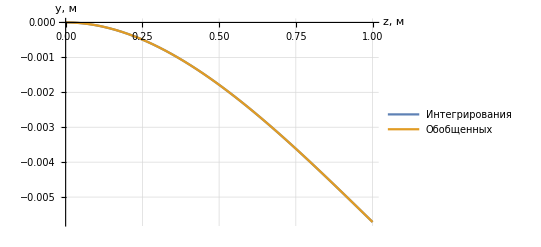

```mathematica
(* Задача 1 *)
(* метод начальных условий*)
pppp  =Plot[{P/(EE J1)(z^3/6-l z^2/2), P/(EE J1)(z^3/6-l z^2/2)},{z, 0, l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic, PlotLegends->{"Интегрирования","Обобщенных"}]
```

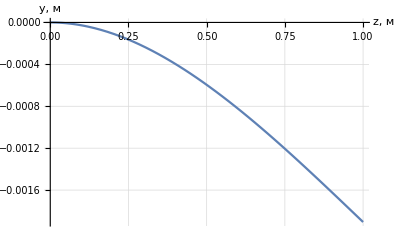

```mathematica
Plot[P/(EE J2)(z^3/6-l z^2/2),{z, 0, l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

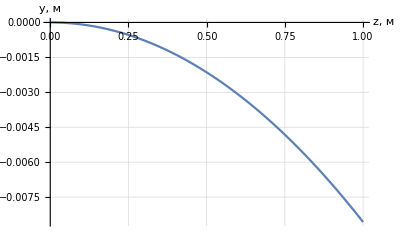

```mathematica
(* метод обобщенных функций *)
CONSOLE[L_, J_]:=Plot[P/(EE J)((z-L)^3/6 H[z, L]-L z^2/2 ),{z, 0, l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
(*
функция для показа графика изгиба балки в консоле, на которую действует сила P на растоянии L отт стены.
примичание: L должна быть меньше длинны балки l
*)
CONSOLE[l, J1]
```

```mathematica
(* Задача 2 *)
(* метод начальных условий*)
```

```mathematica
A = (c2 ==0);
B =( l^3/3-l^2/6+c3 l + c4 ==0);
K := (a^3/2-a^3/(4l) + c3 a + c4 == 1/18 a^3 + c1 a + c2);
M := (a^2 -a^2/(2 l)+c3==b/(2l)a^2+c1 );
```

```mathematica
res =Solve[{A, B,K, M}, {c1, c2, c3, c4}]/.a->2/3 l /. b -> 1/3 l;
cc1 = res[[1, 1, 2]];
cc2 =  res[[1, 2, 2]];
cc3 =  res[[1, 3, 2]];
cc4 =  res[[1, 4, 2]];
```

```mathematica
y1=P/(EE J)(1/18 z^3+cc1 z + cc2)/.J ->J1;
y2= P/(EE J) (l z^2 / 3 - z^2 l/6 + cc3 z + cc4)/.J ->J1;
```

```mathematica
gr1 = Plot[{y1},{z, 0,2/3 l}, PlotStyle->{Orange}];
gr2= Plot[{y2},{z, 2/3 l,l}, PlotStyle->{Orange}];
```

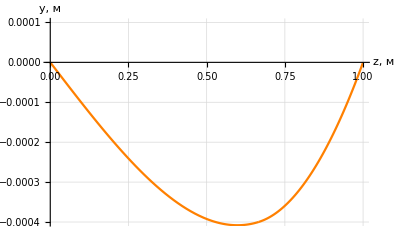

```mathematica
Show[{gr1,gr2}, PlotRange->{{0,l},{-0.0004,0.0001}},  AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

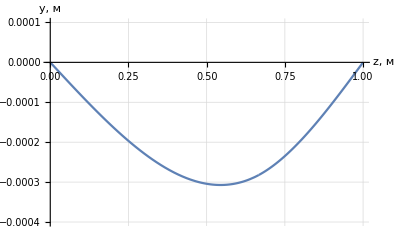

```mathematica
yy2 = P / ( 6 EE J1) 2/3(-z^3+3 z^2 l - z (2 l^2 + 4/9 l^2)+4/9 l^4);
yy1=P / ( 6 EE J1) 1/3(z^3-z 2/3 l (2 l -2/3 l));
gr3 =  Plot[{yy1},{z, 0,2/3 l}];
gr4 = Plot[{yy2},{z, 2/3 l,l}];
Show[gr3, gr4, PlotRange->{{0,l},{-0.0004,0.0001}}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

```mathematica
(* метод обобщенных функций *)
ANGLE111[z_, L_]:=Solve[PP/(EEE JJ)((L ll(z)^3)/6-H[z, l L](z- ll L)^3/6)+coeff z ==0, coeff];

ANGLE111[l, 2/3];
1/(z E1 JJ / (p (b/6  z^3 / L - ((z - a / L)^3)/6)) ) /. z -> L
```

(((b L^2)/6-1/6 (-a/L+L)^3) p)/(E1 JJ L)

```mathematica
FullSimplify[(((b L^2)/6-1/6 (-a/L+L)^3) p)/(E1 JJ L)]
```

((b L^2+((a-L^2)^3)/L^3) p)/(6 E1 JJ L)

```mathematica
((b L^2+((a-L^2)^3)/L^3) p)/(6 E1 JJ L)
FullSimplify[((a-L^2)^3)/L^3]
```

((b L^2+((a-L^2)^3)/L^3) p)/(6 E1 JJ L)

((a-L^2)^3)/L^3

```mathematica
ANGLE[z_, L_]:=Solve[P/(EE J1)((l L(z)^3)/6-H[z, l L](z-l L)^3/6)+coeff z==0, coeff]
(*ANGLE[z_, L_]:=Solve[P/(EE J1)((l L(z)^2)/2-H[z, l L](z-l L)^2/2)+coeff ==0, coeff]*)
(* функция рассчета угла наклона при z == l *)
BEARING[L_, J_]:= Plot[{P/(EE J)((l L(z)^3)/6-H[z, l L](z-l L)^3/6)+ANGLE[l, L][[1, 1, 2]] z},{z, 0,l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
(*
функция для показа графика изгиба балки, лежащую на двух опорах, на которую действует сила P на растоянии L от левой опоры.
примичание: L должна быть меньше длинны балки l
*)
```

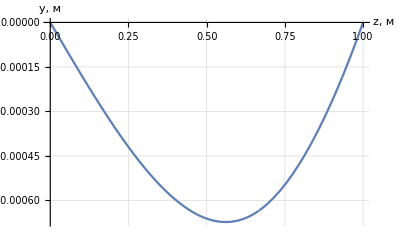

```mathematica
BEARING[2/3, J1]
```

```mathematica
(*сравним результаты*)
BEARING1[L_, J_]:= Plot[{P/(EE J)((z)^3/6(l-L)-H[z, l L](z-l L)^3/6)-ANGLE[l, L][[1, 1, 2]] z},{z, 0,2/3 l}, PlotStyle->Directive[Red,Thick], AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

```mathematica
BEARING2[L_, J_]:= Plot[{P/(EE J)((z)^3/6(l-L)-H[z, l L](z-l L)^3/6)-ANGLE[l, L][[1, 1, 2]] z},{z, 2/3 l,l},PlotStyle->Directive[Red,Thick], AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

```mathematica
(*создали вспомогательные функции, чтобы разбить график на 2 части*)
```

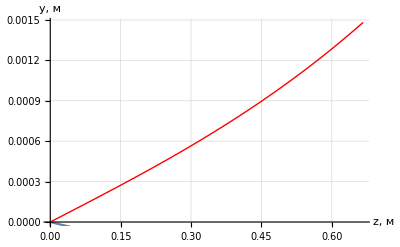

```mathematica
Show[BEARING1[2/3, J1], gr3]
```

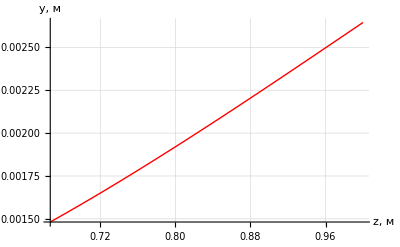

```mathematica
Show[BEARING2[2/3, J1], gr4]
```

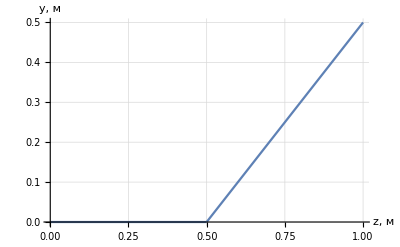

```mathematica
Plot[{(z-0.5) H[z, 0.5]},{z, 0,l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```

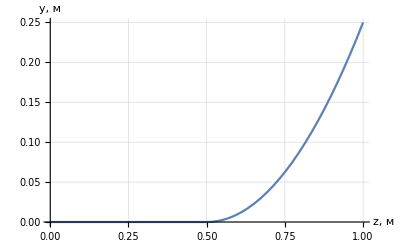

```mathematica
Plot[{((z-0.5)^2) H[z, 0.5]},{z, 0,l}, AxesLabel->{"z, м","y, м"}, GridLines->Automatic]
```